```mathematica
ClearAll[klyshko,klyshkoInf];
klyshko[n_Integer]:=(n!P[n])^2-(n-1)!(n+1)!P[n-1]P[n+1];
klyshko[n_Integer,probs_List]:=(n!probs⟦n+1⟧)^2-(n-1)!(n+1)!probs⟦n⟧probs⟦n+2⟧;
klyshkoInf[n_Integer]:=Sum[P[k],{k,0,n-2}]+((n-1)!P[n-1])^n/((n)!P[n])^(n-1)(ⅇ^((n! P[n])/((n-1)!P[n-1]))-Sum[1/(k!)((n!P[n])/((n-1)!P[n-1]))^k,{k,0,n-2}]);
klyshkoInf[n_Integer,probs_List]:=Sum[probs⟦k+1⟧,{k,0,n-2}]+((n-1)!probs⟦n⟧)^n/((n)!probs⟦n+1⟧)^(n-1)(ⅇ^((n! probs⟦n+1⟧)/((n-1)!probs⟦n⟧))-Sum[1/(k!)((n!probs⟦n+1⟧)/((n-1)!probs⟦n⟧))^k,{k,0,n-2}]);
poisson[λ_,n_]:=ⅇ^-λ λ^n/n!;
```

```mathematica
Needs["utilities`"]
Get[FileNameJoin@{NotebookDirectory[],"generalizedKlyshkoCriteria.m"}]

Qprobs[λs_,s_]:=poisson[λs,s]s!
```

```mathematica
classicalStateProbs=0.5poisson[2.,Range[4]]+0.5poisson[3.,Range[4]]
```

{0.210016,0.247356,0.202244,0.129127}

```mathematica
probs1=classicalStateProbs/klyshkoInf[3,classicalStateProbs];
{klyshkoInf[3,probs1],klyshko[1,probs1],klyshko[2,probs1]}
```

{1.,-0.0303741,-0.0358288}

## Generate random classical state and check that they all satisfy Klyshko’s inequalities

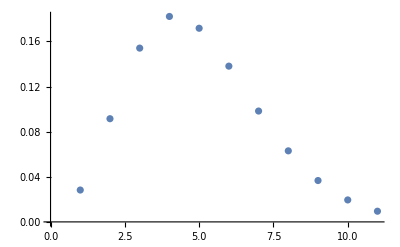

```mathematica
classicalStateMixture[weights_List,λs_List,dimension_Integer]:=Total[weights*Table[poisson[λ,Range[0,dimension]],{λ,λs}]];
randomProbabilityVectors[dim_Integer,numSamples_Integer]:=RandomPoint[Simplex[IdentityMatrix@dim],numSamples]
classicalStateMixture[{0.5,0.5},{3,5},10]//ListPlot
```

```mathematica
bunchOfRandomClassicalStatesOver2lambdas=With[{numStates=1000},
Table[classicalStateMixture[probs,lambdas,4],{probs,randomProbabilityVectors[2,numStates]},{lambdas,RandomReal[{0,4},{numStates,2}]}]
]//Flatten[#,1]&;
bunchOfRandomClassicalStatesOver4lambdas=With[{numStates=100},
Table[classicalStateMixture[probs,lambdas,4],{probs,randomProbabilityVectors[2,numStates]},{lambdas,RandomReal[{0,10},{numStates,2}]}]
]//Flatten[#,1]&;
```

```mathematica
bunchOfRandomClassicalStatesOver4lambdas=With[{numStates=100,numLambdas=4},
Table[classicalStateMixture[probs,lambdas,4],{probs,randomProbabilityVectors[numLambdas,numStates]},{lambdas,RandomReal[{0,10},{numStates,numLambdas}]}]
]//Flatten[#,1]&;
```

```mathematica
bunchOfRandomClassicalStatesOver2lambdas//Dimensions
```

{1000000,5}

## Show that a naive application of the Klyshkos does not give the correct boundary already in (P_0,P_1,P_2,P_3)

What is the boundary of classical states when Q_1^2=Q_0 Q_2 and Q_0+Q_1+Q_2^3/Q_3^2(ⅇ^(Q_3/Q_2)-1-Q_3/Q_2)=1?
We we use the former identity in the latter, and plot the resulting surface, together with the Q_2^2=Q_1 Q_3 one.

```mathematica
Show[ContourPlot3D[
{p1^2/(2p2)+p1+(2p2)^3/(3!p3)^2(ⅇ^((3!p3)/(2p2))-1-(3!p3)/(2p2))==1
,(2p2)^2==p1(3!p3)},
{p1,0,.4},{p2,0,.3},{p3,0,.3},PlotRange->All,AxesLabel->{1,2,3}],
ParametricPlot3D[ⅇ^-λ λ^{1,2,3}/{1,2,3}!,{λ,0,20},PlotStyle->{Black}]
]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[
{p1^2/(2p2)+p1+(2p2)^3/(3!p3)^2(ⅇ^((3!p3)/(2p2))-1-(3!p3)/(2p2))==1
(*,(2p2)^2==p1(3!p3)*)},
{p1,0,.4},{p2,0,.3},{p3,0,.3},PlotRange->{{0,0.4},{0,0.3},{0,0.3}},AxesLabel->{1,2,3},ContourStyle->Opacity[0.5]],
ParametricPlot3D[{ⅇ^-λ λ^{1,2,3}/{1,2,3}!},{λ,0,20},PlotStyle->{Black}]
(*,ParametricPlot3D[{(4 t2^2)/(6 t3),t2,t3},{t2,0,.3},{t3,0.001,.3},PlotStyle->{Red}]*)
,Graphics3D[{
Point@bunchOfRandomClassicalStatesOver4lambdas⟦;;10000,{2,3,4}⟧
}]
]
```

-Graphics3D-

```mathematica
Show[ContourPlot3D[
{p1^2/(2p2)+p1+(2p2)^3/(3!p3)^2(ⅇ^((3!p3)/(2p2))-1-(3!p3)/(2p2))==1
,(2p2)^2==p1(3!p3)},
{p1,0,.4},{p2,0,.3},{p3,0,.3},PlotRange->All,AxesLabel->{1,2,3},ContourStyle->{Directive[Opacity[0.4]],Directive[Opacity@1]}],
ParametricPlot3D[ⅇ^-λ λ^{1,2,3}/{1,2,3}!,{λ,0,20},PlotStyle->{Black}],
Graphics3D[{Black,
Point@bunchOfRandomClassicalStatesOver4lambdas⟦;;10000,{2,3,4}⟧
}]
]
```

Notice that the surface obtained by intersection of K_1 and K_∞ doesn’t seem to equal the convex hull of the classical states, which would mean that there are nonclassical states satisfying Klyshkos’ inequalities. To check this, we find the normal vector to this surface at a point that, numerically, classical states don’t seem to reach. Once we have this point, we can find the boundary using the linear functional maximisation method

```mathematica
expr=p1^2/(2p2)+p1+(2p2)^3/(3!p3)^2(ⅇ^((3!p3)/(2p2))-1-(3!p3)/(2p2))-1;
Reduce[expr==0,p1]/.{p2->0.15,p3->0.15}
```

p1==-0.552051||p1==0.252051

We want to find a local parametrisation for the surface at the point p_2=0.15, p_3=0.15. The second solution given by solving for p_1 seems to be the one we are looking for

```mathematica
Reduce[expr==0,p1]//Last//Last//#/.{p2->0.15,p3->0.15}&
```

p1==0.252051

```mathematica
Reduce[expr==0,p1]
```

p3≠0&&p2≠0&&(p1==(-3 p2 p3^2-√(4 p2^4 p3^2-4 ⅇ^((3 p3)/p2) p2^4 p3^2+12 p2^3 p3^3+18 p2 p3^4+9 p2^2 p3^4))/(3 p3^2)||p1==(-3 p2 p3^2+√(4 p2^4 p3^2-4 ⅇ^((3 p3)/p2) p2^4 p3^2+12 p2^3 p3^3+18 p2 p3^4+9 p2^2 p3^4))/(3 p3^2))

```mathematica
parametrisation={(-3 p2 p3^2+√(4 p2^4 p3^2-4 ⅇ^((3 p3)/p2) p2^4 p3^2+12 p2^3 p3^3+18 p2 p3^4+9 p2^2 p3^4))/(3 p3^2),p2,p3}
```

{(-3 p2 p3^2+√(4 p2^4 p3^2-4 ⅇ^((3 p3)/p2) p2^4 p3^2+12 p2^3 p3^3+18 p2 p3^4+9 p2^2 p3^4))/(3 p3^2),p2,p3}

```mathematica
normalVectorExpr=Cross[D[parametrisation,p2]//Simplify,D[parametrisation,p3]//Simplify]//FullSimplify;
normalVectorAtPoint=normalVectorExpr/.{p2->0.15,p3->0.15}//Normalize
```

{0.379436,-0.482979,0.789151}

```mathematica
normalVectorAtPoint*poisson[λ,{1,2,3}]//Total//Maximize[{#,λ≥0},λ,Reals]&
```

{0.125321,{λ→2.93903}}

This is saying that the classical state with λ≃2.93 corresponds to the vector tangent to the given point, and that this plane has distance 0.125 from the origin.
In the next figure, we show the surface corresponding to K_1∩K_∞ in the (P_1,P_2,P_3) space, together with a bunch of simulated classical states, and the plane tangent to the classical states at the point λ=2.93. This plane is ensured to touch the boundary of the classical set, and the fact that from the plot it’s clear that there are points compatible with K_1∩K_∞ that lie beyond the plane, proves that Klyshko’s inequalities are not enough to characterise the region in this space.

```mathematica
Show[ContourPlot3D[
{p1^2/(2p2)+p1+(2p2)^3/(3!p3)^2(ⅇ^((3!p3)/(2p2))-1-(3!p3)/(2p2))==1},
{p1,0,.4},{p2,0,.3},{p3,0,.3},PlotRange->{{0,0.4},{0,0.3},{0,0.3}},AxesLabel->{1,2,3},ContourStyle->Opacity[0.5]],
ParametricPlot3D[{ⅇ^-λ λ^{1,2,3}/{1,2,3}!},{λ,0,20},PlotStyle->{Black}]
,Graphics3D[{
Point@bunchOfRandomClassicalStatesOver4lambdas⟦;;10000,{2,3,4}⟧,
{Red,PointSize@0.01,Point@poisson[2.939,{1,2,3}]}
}]
,ContourPlot3D[Total[normalVectorAtPoint*{x,y,z}]==0.125//Evaluate,{x,0,1},{y,0,1},{z,0,1}]
]
```

-Graphics3D-

```mathematica
klyshkoInf[3]
```

P[0]+P[1]+(2 P[2]^3 (-1+ⅇ^((3 P[3])/P[2])-(3 P[3])/P[2]))/(9 P[3]^2)

Assume for a moment that the value of P_0 is known (it has been measured or whatever). Can we then characterise the associated geometric structure of the classical space in the other probabilities (P_1,P_2,P_3)?

```mathematica
assumedP0=0.4;
Show[ContourPlot3D[{
4 p2^2==6p1 p3
,assumedP0+p1+(2 p2^3(ⅇ^(3p3/p2)-3p3/p2-1))/(9 p3^2)==1
(*,p1^3==6p3 assumedP0^2
,p1^2==2p2 assumedP0*)
},{p1,0,1},{p2,0,.3},{p3,0,.3},PlotRange->All,AxesLabel->{1,2,3},PlotLegends->Automatic,ContourStyle->Opacity[0.8]] 
,ParametricPlot3D[ⅇ^-λ λ^{1,2,3}/{1,2,3}!,{λ,0,20},PlotStyle->{Black}]]
```

-Graphics3D-

## Set of classical states in the P_0,P_1,P_3 space